### Defining model parameters and drug kinetics

```mathematica
λ= 2*10^6;d=2*0.05;β =5* 10^-10;c=10.0;a=0.5;u= 3 * 10^-5;k=1000.0;R=(λ β k)/(d a c) ;
Subscript[y, 0]=λ/a-(d * c)/(β k);
Subscript[x, 0]=λ/d;
```

```mathematica
R
```

2.

```mathematica
ϵ[eavg_,A_,T_,t_]:=ϵ[eavg,A,T,t]=eavg-A*Cos[(2*Pi)/T t]
```

### Deterministic dynamics of target and WT infected cells after the onset of treatment

```mathematica
solution[evg_,A_,T_]:=NDSolve[{xf'[tf]==λ-d xf[tf]-(β k)/c(1-ϵ[evg,A,T,tf])xf[tf]yf[tf],yf'[tf]==(β k)/c(1-ϵ[evg,A,T,tf])xf[tf]yf[tf]-a yf[tf],xf[0]==Subscript[x, 0]/2,yf[0]== Subscript[y, 0]},{xf,yf},{tf,0,500}]
```

```mathematica
xfull[tf_,evg_,A_,T_]:=xf[tf]/.solution[evg,A,T][[1]];
yfull[tf_,evg_,A_,T_]:=yf[tf]/.solution[evg,A,T][[1]];
```

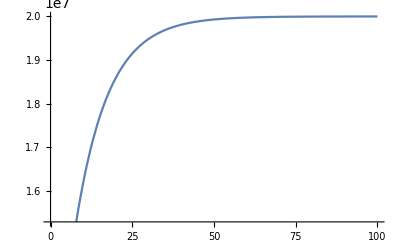

```mathematica
Plot[xfull[t,0.9,0.09,1],{t,0,100}]
```

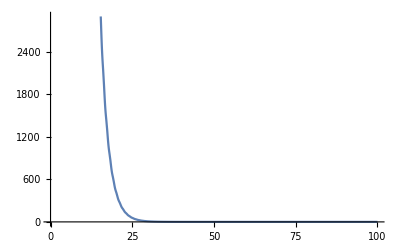

```mathematica
Plot[yfull[t,0.9,0.09,1],{t,0,100}]
```

### Establishment probability of a pre-existing mutant

Calculated as a time-dependent birth-death process

```mathematica
Birth[s_,As_,eavgs_,Ar_,eavgr_,T_,tp_]:=Birth[s,As,eavgs,Ar,eavgr,T,tp]= Re[(1-s)* β*k/c*xfull[tp,eavgs,As,T]*(1-ϵ[eavgr,Ar,T,tp])]
```

```mathematica
r1[s_,As_,eavgs_,Ar_,eavgr_,T_,t_,τ_?NumericQ]:=r1[s,As,eavgs,Ar,eavgr,T,t,τ]=NIntegrate[a-Birth[s,As,eavgs,Ar,eavgr,T,tp],{tp,t,τ},Method->{"GaussKronrodRule","SymbolicProcessing"->0}, WorkingPrecision-> 5]
```

```mathematica
pest[s_,As_,eavgs_,Ar_,eavgr_,T_,t_?NumericQ]:=pest[s,As,eavgs,Ar,eavgr,T,t]=1/(1+NIntegrate[Exp[r1[s,As,eavgs,Ar,eavgr,T,t,τ]],{τ,t,t+150},Method->{"GaussKronrodRule","SymbolicProcessing"->0}, WorkingPrecision->5]*a)
```

#### Full resistance

Establishment probability for constant drug efficacy equal to the time averaged efficacy

```mathematica
pest[0.3, 0.0, 0.9, 0.0,0.0, 1,0]
```

0.0759033

Establishment probability for constant drug efficacy equal to the efficacy at t=0

```mathematica
pest[0.3, 0.0, 0.9 - 0.09, 0.0,0.0, 1,0]
```

0.0726884

Establishment probability on varying the drug dosing period from T=1, to T=200

```mathematica
Table[pest[0.3,0.09,0.9,0.0,0.0,T,0],{T,1,200,4}]
```

{0.0758863,0.0755607,0.0749817,0.0744284,0.0740056,0.073703,0.0734871,0.0733303,0.0732138,0.0731253,0.0730569,0.0730029,0.0729597,0.0729247,0.0728959,0.0728719,0.0728518,0.0728348,0.0728202,0.0728077,0.0727969,0.0727875,0.0727792,0.0727719,0.0727654,0.0727597,0.0727545,0.0727499,0.0727458,0.0727421,0.0727387,0.0727356,0.0727328,0.0727302,0.0727279,0.0727257,0.0727237,0.0727219,0.0727202,0.0727186,0.0727171,0.0727158,0.0727145,0.0727133,0.0727122,0.0727112,0.0727103,0.0727093,0.0727085,0.0727077}

#### Partial resistance

Establishment probability for constant drug efficacy equal to the time averaged efficacy

```mathematica
pest[0.3, 0.0, 0.9, 0.0,0.099, 1,0]
```

0.0421366

Establishment probability for constant drug efficacy equal to the efficacy at t=0

```mathematica
pest[0.3, 0.0, 0.9-0.09, 0.0,0.099-0.09, 1,0]
```

0.069531

Establishment probability on varying the drug dosing period from T=1, to T=200

```mathematica
Table[pest[0.3,0.09,0.9,0.09,0.099,T,0],{T,1,200,4}]
```

{0.0417703,0.0415115,0.0413773,0.0407135,0.0428054,0.0395374,0.0392338,0.0392345,0.0395796,0.0401857,0.0410721,0.0421676,0.0434214,0.0447858,0.0462175,0.0476798,0.0491405,0.0505736,0.0519594,0.0532816,0.0545304,0.0556992,0.056785,0.0577875,0.0587083,0.0595508,0.0603191,0.0610182,0.0616533,0.0622296,0.0627524,0.0632266,0.0636569,0.0640477,0.064403,0.0647264,0.0650212,0.0652903,0.0655364,0.0657619,0.0659689,0.0661593,0.0663347,0.0664966,0.0666463,0.066785,0.0669138,0.0670335,0.067145,0.067249}

### Risk of resistance due to rescue mutants

The risk is calculated by treating the process as a time-inhomogeneous Poisson process.

Correction term for setting the free pathogen population proportional to the infected cell population

```mathematica
m1[evg_,A_]:=m1[evg,A]=(1-evg+A)(u Subscript[y, 0] a)/c;
```

Rate at which rescue mutants are produced

```mathematica
ν[s_,As_,eavgs_,Ar_,eavgr_,T_,t_]:=ν[s,As,eavgs,Ar,eavgr,T,t]=((β k)/c(1-ϵ[eavgs,As,T,t])u)xfull[t,eavgs,As,T]yfull[t,eavgs,As,T]pest[s,As,eavgs,Ar,eavgr,T,t]
```

```mathematica
Subscript[Int, resc][s_,As_,eavgs_,Ar_,eavgr_,T_,tfin_]:= NIntegrate[1/d ν[s,As,eavgs,Ar,eavgr,T,t/d],{t,0,tfin},WorkingPrecision-> 5, Method->{"GaussKronrodRule","SymbolicProcessing"->0}]
```

Probability that at least one rescue mutant is produced

```mathematica
Subscript[P, resc][s_,As_,eavgs_,Ar_,eavgr_,T_]:=1-Exp[-m1[eavgs,As]pest[s,As,eavgs,Ar,eavgr,T,0]-Subscript[Int, resc][s,As,eavgs,Ar,eavgr,T,10]]
```

#### Full resistance

Rescue probability for drug efficacy equal to the time-average

```mathematica
Subscript[P, resc][0.3,0.0,0.9,0,0,1]
```

0.595044

Rescue probability for a constant drug efficacy at t=0

```mathematica
Subscript[P, resc][0.3,0.0,0.9-0.09,0,0,1]
```

0.864021

Rescue probability on varying the drug dosing period from T=1 to T=150

```mathematica
Table[Subscript[P, resc][0.3,0.09,0.90,0,0,n],{n,1,21,4}]
```

{0.605178,0.614,0.640394,0.67827,0.715647,0.74614}

```mathematica
Table[Subscript[P, resc][0.3,0.09,0.90,0,0,n],{n,25,150,10}]
```

{0.769337,0.8053,0.824312,0.835446,0.842506,0.847259,0.850608,0.853054,0.854894,0.856311,0.857426,0.858317,0.859041}

#### Partial resistance

Rescue probability for drug efficacy equal to the time-average

```mathematica
Subscript[P, resc][0.3,0.0,0.90,0,0.099,1]
```

0.413621

Rescue probability for a constant drug efficacy at t = 0

```mathematica
Subscript[P, resc][0.3,0.0,0.90-0.09,0,0.099-0.09,1]
```

0.853396

Rescue probability on varying the drug dosing period from T=1 to T=150

```mathematica
Table[Subscript[P, resc][0.3,0.09,0.90,0.09,0.099,n],{n,1,21,4}]
```

{0.421683,0.427054,0.437577,0.466712,0.493043,0.51639}

```mathematica
Table[Subscript[P, resc][0.3,0.09,0.90,0.09,0.099,n],{n,25,150,10}]
```

{0.535873,0.578439,0.619752,0.661025,0.699366,0.731301,0.757065,0.777005,0.792202,0.803723,0.812489,0.81922,0.824451}